## Flux Basis

```mathematica
Llist[g_,L_] := Table [ - g^2/(2) ,2 L] 
 Ldown[g_,L_] := DiagonalMatrix[Llist[g,L],1]
Lup[g_,L_] := DiagonalMatrix[Llist[g,L],-1]
LzLz[g_,L_] := DiagonalMatrix[Table[m^2 /g^2  +  g^2,{m,-L, L }] ]
FluxPlaqOperator[g_,L_]  := LzLz[g,L]+  Ldown[g,L]+  Lup[g,L]
```

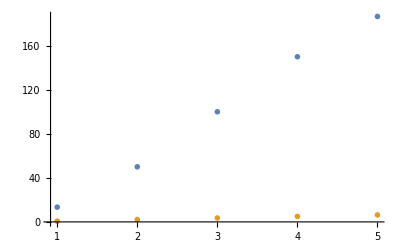

```mathematica
L=2;
g=10;
ListPlot[{Sort[Eigenvalues[FluxPlaqOperator[g,L]//N]//N, Less], Sort[Eigenvalues[FluxPlaqOperator[g,200]//N]//N, Less][[1;;2L+1]]}, PlotRange->All, PlotMarkers->{{"o", Large}, {"x", Large}}, PlotRange->All]
```

```mathematica
Eigenvalues[FluxPlaqOperator[1,2]//N]//N
```

{5.0844,5.08114,2.29401,1.91886,0.621589}

## Qubit

```mathematica
(*Sigma operators*)
```

```mathematica
Sigma[0] = SparseArray[IdentityMatrix[2]];
Sigma[1] = SparseArray[{{0, 1}, {1, 0}}];
Sigma[2] = SparseArray[{{0, -I}, {I, 0}}];
Sigma[3] = SparseArray[{{1, 0}, {0, -1}}];
Sigma[4]= (Sigma[1]+ I*Sigma[2])/2;
Sigma[5]= (Sigma[1]- I*Sigma[2])/2;
```

```mathematica
(* Kronecker builds multi-Qubit tensor:  Left most matrix has fast  -- low bit -- convention 
Lables of N = nQubit tensor should be   sigma_{N} x sigma_{N-1} x  ... x  sigma_{0}   *)
```

```mathematica
(* Insert FullSigma[ a = sigma_type , j = postion = 0,1,..., nQubit-1] *)
```

```mathematica
FullSigma[ a_, j_, nQubit_]:=SparseArray[KroneckerProduct[IdentityMatrix[2^(nQubit-j -1)], Sigma[a], IdentityMatrix[2^j]]]
MatrixForm[FullSigma[3, 1, 2]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

### The U(1) plaquette in qubit representation

```mathematica
HKinetic[M_, g_]:=(1/g^2)Sum[FullSigma[3, m, M], {m, 0, M-1}]^2
MatrixForm[HKinetic[4, 1]]
```

(16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16)

```mathematica
Partitions[list_]:=FoldPairList[TakeDrop,list,#]&/@Flatten[Permutations/@IntegerPartitions[Length[list]],1]
Partitions[Range[3]]
Map[Last, Partitions[Range[3]], {2}]
```

{{{1,2,3}},{{1,2},{3}},{{1},{2,3}},{{1},{2},{3}}}

{{3},{2,3},{1,3},{1,2,3}}

```mathematica
Subsets[Range[3], {1, 3}]
```

{{1},{2},{3},{1,2},{1,3},{2,3},{1,2,3}}

```mathematica
SigmaList[list_, M_, kind_]:=(
pList = ConstantArray[0,M]; 
pList[[list]]=kind;Return[KroneckerProduct@@Table[Sigma[pList[[i]]], {i, 1, Length[pList]}]])
HPotential[M_, g_]:=
(g^2/2)Sum[FullSigma[4, l, M]+FullSigma[5, l, M], {l, 0, M-1}]2/M
(*HPotential[M_, g_]:=
(g^2/2)2Sum[Sum[SigmaList[Subsets[Range[M], {l}][[i]], M, 4]+SigmaList[Subsets[Range[M], {l}][[i]], M, 5], {i, 1, Length[Subsets[Range[M], {l}]]}]/Length[Subsets[Range[M], {l}]], {l, 1, 1}]*)
(*HPotential[M_, g_]:=(
ListSupports = Map[Last, Partitions[Range[M]], {2}];
Return[(g^2/2)Sum[Sum[SigmaList[Select[ListSupports, Length[#]==l&][[i]], M, 4]+SigmaList[Select[ListSupports, Length[#]==l&][[i]], M, 5], {i, 1, Length[Select[ListSupports, Length[#]==l&]]}]/Length[Select[ListSupports, Length[#]==l&]], {l, 1, M}]])*)
```

```mathematica
H[M_, g_]:=HKinetic[M, g]/4- HPotential[M, g]+g^2IdentityMatrix[2^M]
```

```mathematica
(* The action of the potential term does not give a normalized state*)
```

```mathematica
MatrixForm[Table[Norm[Sum[FullSigma[4, l, M], {l, 0, M-1}].SingletStates[[i]]], {i, 1, M+1}]]//FullSimplify
```

(0
2
√6
√6
2)

```mathematica
M=8;
g=100;
SingletStates = Table[(1/Sqrt[Binomial[M, PartN]])Sum[If[Total[IntegerDigits[n, 2]]==PartN, SparseArray[Table[If[i==n, 1, 0], {i, 0, 2^M-1}]], 0], {n, 0, 2^M-1}], {PartN, 0, M}];SymmetricSubH= Table[SingletStates[[i]].H[M, g].SingletStates[[j]], {i, 1, M+1}, {j, 1, M+1}]//N;
MatrixForm[SymmetricSubH]
MatrixForm[FluxPlaqOperator[g, M/2]]
```

(SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…]
SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…]
SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…]
SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…]
SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…]
SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…]
SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…]
SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…]
SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…] | SparseArray[…].H[8.,100.].SparseArray[…])

(6250001/625 | -5000 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-5000 | 100000009/10000 | -5000 | 0 | 0 | 0 | 0 | 0 | 0
0 | -5000 | 25000001/2500 | -5000 | 0 | 0 | 0 | 0 | 0
0 | 0 | -5000 | 100000001/10000 | -5000 | 0 | 0 | 0 | 0
0 | 0 | 0 | -5000 | 10000 | -5000 | 0 | 0 | 0
0 | 0 | 0 | 0 | -5000 | 100000001/10000 | -5000 | 0 | 0
0 | 0 | 0 | 0 | 0 | -5000 | 25000001/2500 | -5000 | 0
0 | 0 | 0 | 0 | 0 | 0 | -5000 | 100000009/10000 | -5000
0 | 0 | 0 | 0 | 0 | 0 | 0 | -5000 | 6250001/625)

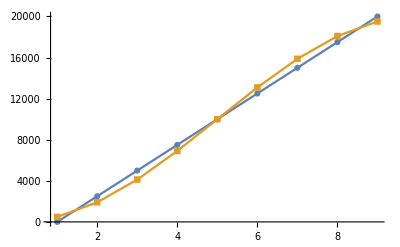

```mathematica
ListPlot[{Sort[Eigenvalues[SymmetricSubH]//N, Less], Sort[Eigenvalues[FluxPlaqOperator[g,M/2]//N]//N, Less]},PlotRange->All, Joined->True, PlotMarkers->Automatic]
```

```mathematica
QubitSymH[M_, g_]:=DiagonalMatrix[Table[m^2 /g^2  +  g^2,{m,-M, M}] ]+g^2/2DiagonalMatrix[Join[Table[-Sqrt[m(2M-m+1)]/M,{m,1, M }], Reverse[Table[-Sqrt[m(2M-m+1)]/M,{m,1, M}]]],1 ]+g^2/2DiagonalMatrix[Join[Table[-Sqrt[m(2M-m+1)]/M,{m,1, M }], Reverse[Table[-Sqrt[m(2M-m+1)]/M,{m,1, M}]]],-1 ]
MatrixForm[QubitSymH[2, 10]]//N
```

(100.04 | -50. | 0. | 0. | 0.
-50. | 100.01 | -61.2372 | 0. | 0.
0. | -61.2372 | 100. | -61.2372 | 0.
0. | 0. | -61.2372 | 100.01 | -50.
0. | 0. | 0. | -50. | 100.04)

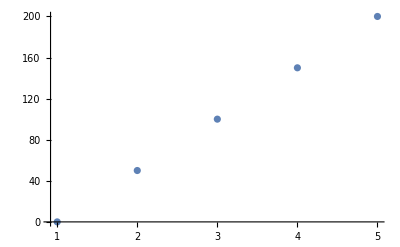

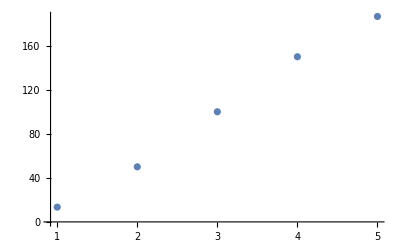

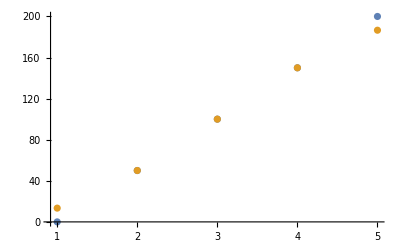

```mathematica
g=10;
M=2;
ListPlot[Sort[Eigenvalues[QubitSymH[M, g]//N]//N, Less],PlotRange->All]
ListPlot[Sort[Eigenvalues[FluxPlaqOperator[g,M]//N]//N, Less],PlotRange->All]
ListPlot[{Sort[Eigenvalues[QubitSymH[M, g]//N]//N, Less], Sort[Eigenvalues[FluxPlaqOperator[g,M]//N]//N, Less]},PlotRange->All]
(*Animate[ListPlot[{Sort[Eigenvalues[QubitSymH[M, 10^g]//N]//N, Less], Sort[Eigenvalues[FluxPlaqOperator[10^g,M]//N]//N, Less]},PlotRange->All, Joined->True], {g, -2, 3}]*)
```

```mathematica
M=2;
SingletStates = Table[(1/Sqrt[Binomial[M, PartN]])Sum[If[Total[IntegerDigits[n, 2]]==PartN, SparseArray[Table[If[i==n, 1, 0], {i, 0, 2^M-1}]], 0], {n, 0, 2^M-1}], {PartN, 0, M}];
MatrixForm[Table[SingletStates[[i]].H[M, 10].SingletStates[[j]], {i, 1, M+1}, {j, 1, M+1}]//N]
MatrixForm[FluxPlaqOperator[10,M/2]]//N
```

(SparseArray[…].H[2.,10.].SparseArray[…] | SparseArray[…].H[2.,10.].SparseArray[…] | SparseArray[…].H[2.,10.].SparseArray[…]
SparseArray[…].H[2.,10.].SparseArray[…] | SparseArray[…].H[2.,10.].SparseArray[…] | SparseArray[…].H[2.,10.].SparseArray[…]
SparseArray[…].H[2.,10.].SparseArray[…] | SparseArray[…].H[2.,10.].SparseArray[…] | SparseArray[…].H[2.,10.].SparseArray[…])

(100.01 | -50. | 0.
-50. | 100. | -50.
0. | -50. | 100.01)

```mathematica
M=4;
SingletStates = Table[(1/Sqrt[Binomial[M, PartN]])Sum[If[Total[IntegerDigits[n, 2]]==PartN, SparseArray[Table[If[i==n, 1, 0], {i, 0, 2^M-1}]], 0], {n, 0, 2^M-1}], {PartN, 0, M}];
MatrixForm[Table[SingletStates[[i]].H[M, 10].SingletStates[[j]], {i, 1, M+1}, {j, 1, M+1}]//N]
MatrixForm[FluxPlaqOperator[10,M/2]]//N
```

(100.04 | -50. | 0. | 0. | 0.
-50. | 100.01 | -61.2372 | 0. | 0.
0. | -61.2372 | 100. | -61.2372 | 0.
0. | 0. | -61.2372 | 100.01 | -50.
0. | 0. | 0. | -50. | 100.04)

(100.04 | -50. | 0. | 0. | 0.
-50. | 100.01 | -50. | 0. | 0.
0. | -50. | 100. | -50. | 0.
0. | 0. | -50. | 100.01 | -50.
0. | 0. | 0. | -50. | 100.04)

## Check the algebra

```mathematica
Commutator[A_, B_]:=A.B-B.A
```

```mathematica
M=4;
Commutator[Sum[FullSigma[3, l, M], {l, 0, M-1}], Sum[FullSigma[4, l, M], {l, 0, M-1}]]==2Sum[FullSigma[4, l, M], {l, 0, M-1}]//FullSimplify
Commutator[Sum[FullSigma[3, l, M], {l, 0, M-1}], Sum[FullSigma[5, l, M], {l, 0, M-1}]]==-2Sum[FullSigma[5, l, M], {l, 0, M-1}]//FullSimplify
MatrixForm[Commutator[Sum[FullSigma[4, l, M], {l, 0, M-1}], Sum[FullSigma[5, l, M], {l, 0, M-1}]]]
```

True

True

(4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4)

## Goes higher terms

```mathematica
HPotentialHigh[M_, g_]:=
(g^2/2)2Sum[(Factorial[M-2l-1]Factorial[l]Factorial[l+1]/Factorial[M])Sum[Sum[SigmaList[Permutations[Subsets[Range[M], {2l+1}][[i]]][[j]][[1;;l+1]], M, 4].SigmaList[Permutations[Subsets[Range[M], {2l+1}][[i]]][[j]][[l+2;;2l+1]], M, 5]+
SigmaList[Permutations[Subsets[Range[M], {2l+1}][[i]]][[j]][[1;;l+1]], M, 5].SigmaList[Permutations[Subsets[Range[M], {2l+1}][[i]]][[j]][[l+2;;2l+1]], M, 4],{j, 1, Length[Permutations[Subsets[Range[M], {2l+1}][[i]]]]}], {i, 1, Length[Subsets[Range[M], {2l+1}]]}], {l, 0,M/2-1}]
HPotentialHigh[2, 1]==Sum[SigmaList[{i}, 2, 4]+SigmaList[{i}, 2, 5], {i, 1, 2}]/2
```

1/2 (SigmaList[{1},2,4].SigmaList[{},2,5]+SigmaList[{1},2,5].SigmaList[{},2,4]+SigmaList[{2},2,4].SigmaList[{},2,5]+SigmaList[{2},2,5].SigmaList[{},2,4])==1/2 (SigmaList[{1},2,4]+SigmaList[{1},2,5]+SigmaList[{2},2,4]+SigmaList[{2},2,5])

```mathematica
HHigh[M_, g_]:=HKinetic[M, g]/4- HPotentialHigh[M, g]+g^2IdentityMatrix[2^M]
```

```mathematica
M=6;
g=1;
SingletStates = Table[(1/Sqrt[Binomial[M, PartN]])Sum[If[Total[IntegerDigits[n, 2]]==PartN, SparseArray[Table[If[i==n, 1, 0], {i, 0, 2^M-1}]], 0], {n, 0, 2^M-1}], {PartN, 0, M}];SymmetricSubHHigh= Table[SingletStates[[i]].HHigh[M, g].SingletStates[[j]], {i, 1, M+1}, {j, 1, M+1}]//N;
MatrixForm[Table[SingletStates[[i]].H[M, g].SingletStates[[j]], {i, 1, M+1}, {j, 1, M+1}]//N]
MatrixForm[SymmetricSubHHigh]
MatrixForm[FluxPlaqOperator[g, M/2]]
```

(10. | -0.408248 | 0. | 0. | 0. | 0. | 0.
-0.408248 | 5. | -0.527046 | 0. | 0. | 0. | 0.
0. | -0.527046 | 2. | -0.57735 | 0. | 0. | 0.
0. | 0. | -0.57735 | 1. | -0.57735 | 0. | 0.
0. | 0. | 0. | -0.57735 | 2. | -0.527046 | 0.
0. | 0. | 0. | 0. | -0.527046 | 5. | -0.408248
0. | 0. | 0. | 0. | 0. | -0.408248 | 10.)

(10. | -0.408248 | 0. | 0. | 0. | 0. | 0.
-0.408248 | 5. | -0.737865 | 0. | 0. | 0. | 0.
0. | -0.737865 | 2. | -1.61658 | 0. | 0. | 0.
0. | 0. | -1.61658 | 1. | -1.61658 | 0. | 0.
0. | 0. | 0. | -1.61658 | 2. | -0.737865 | 0.
0. | 0. | 0. | 0. | -0.737865 | 5. | -0.408248
0. | 0. | 0. | 0. | 0. | -0.408248 | 10.)

(10 | -1/2 | 0 | 0 | 0 | 0 | 0
-1/2 | 5 | -1/2 | 0 | 0 | 0 | 0
0 | -1/2 | 2 | -1/2 | 0 | 0 | 0
0 | 0 | -1/2 | 1 | -1/2 | 0 | 0
0 | 0 | 0 | -1/2 | 2 | -1/2 | 0
0 | 0 | 0 | 0 | -1/2 | 5 | -1/2
0 | 0 | 0 | 0 | 0 | -1/2 | 10)

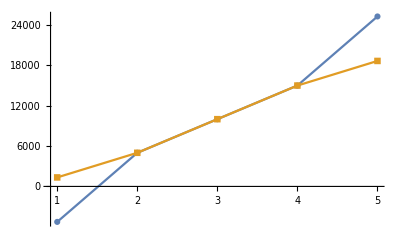

```mathematica
ListPlot[{Sort[Eigenvalues[SymmetricSubHHigh]//N, Less], Sort[Eigenvalues[FluxPlaqOperator[g,M/2]//N]//N, Less]},PlotRange->All, Joined->True, PlotMarkers->Automatic]
```

## Plaq operator found by David for j=2(M=4)

where -Graphics-  and a_k can be computed by solving the LE
 
 where -Graphics-

```mathematica
HExact[M_, g_] := (
(*Solve for the normalization factors*)
A=Table[If[k==0, 1, (l(l+1))^k] Sqrt[(M/2-l)(M/2+l+1)],{l,0, M/2-1}, {k, 0, M/2-1}];
a=Inverse[A].ConstantArray[1, M/2];
Return[HKinetic[M, g]/4-(g^2/2)Sum[a[[k+1]](If[k==0, IdentityMatrix[2^M], MatrixPower[Sum[FullSigma[3, l, M]/2, {l, 0, M-1}], k]].Sum[FullSigma[4, l, M], {l, 0, M-1}].If[k==0, IdentityMatrix[2^M], MatrixPower[Sum[FullSigma[3, l, M]/2, {l, 0, M-1}], k]]+If[k==0, IdentityMatrix[2^M], MatrixPower[Sum[FullSigma[3, l, M]/2, {l, 0, M-1}], k]].Sum[FullSigma[5, l, M], {l, 0, M-1}].If[k==0, IdentityMatrix[2^M], MatrixPower[Sum[FullSigma[3, l, M]/2, {l, 0, M-1}], k]]), {k, 0, M/2-1}]+g^2IdentityMatrix[2^M]])
```

(100.16 | -50. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-50. | 100.09 | -50. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -50. | 100.04 | -50. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -50. | 100.01 | -50. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -50. | 100. | -50. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -50. | 100.01 | -50. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -50. | 100.04 | -50. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -50. | 100.09 | -50.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -50. | 100.16)

(100.16 | -50. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-50. | 100.09 | -50. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -50. | 100.04 | -50. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -50. | 100.01 | -50. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -50. | 100. | -50. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -50. | 100.01 | -50. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -50. | 100.04 | -50. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -50. | 100.09 | -50.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -50. | 100.16)

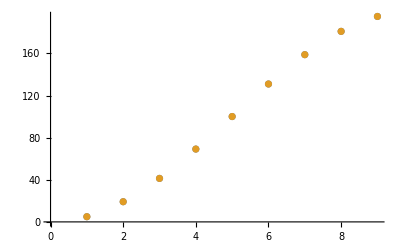

```mathematica
M=8;
g=10;
SingletStates = Table[(1/Sqrt[Binomial[M, PartN]])Sum[If[Total[IntegerDigits[n, 2]]==PartN, SparseArray[Table[If[i==n, 1, 0], {i, 0, 2^M-1}]], 0], {n, 0, 2^M-1}], {PartN, 0, M}];
SymmetricSubH= Table[SingletStates[[i]].HExact[M, g].SingletStates[[j]], {i, 1, M+1}, {j, 1, M+1}]//N;
MatrixForm[SymmetricSubH]
MatrixForm[FluxPlaqOperator[g, M/2]//N]
ListPlot[{Sort[Eigenvalues[SymmetricSubH//N], Less], Sort[Eigenvalues[FluxPlaqOperator[g, M/2]//N], Less]}]
```

## Check [U, U^\dag]

```mathematica
U[M_] := (
(*Solve for the normalization factors*)
A=Table[If[k==0, 1, (4l(l+1))^k] Sqrt[(M/2-l)(M/2+l+1)],{l,0, M/2-1}, {k, 0, M/2-1}];
a=Inverse[A].ConstantArray[1, M/2];
Return[Sum[a[[k+1]]If[k==0, IdentityMatrix[2^M], MatrixPower[Sum[FullSigma[3, l, M], {l, 0, M-1}], k]].Sum[FullSigma[4, l, M], {l, 0, M-1}].If[k==0, IdentityMatrix[2^M], MatrixPower[Sum[FullSigma[3, l, M], {l, 0, M-1}], k]], {k, 0, M/2-1}]])
Udag[M_] := (
(*Solve for the normalization factors*)
A=Table[If[k==0, 1, (4l(l+1))^k] Sqrt[(M/2-l)(M/2+l+1)],{l,0, M/2-1}, {k, 0, M/2-1}];
a=Inverse[A].ConstantArray[1, M/2];
Return[Sum[a[[k+1]]If[k==0, IdentityMatrix[2^M], MatrixPower[Sum[FullSigma[3, l, M], {l, 0, M-1}], k]].Sum[FullSigma[5, l, M], {l, 0, M-1}].If[k==0, IdentityMatrix[2^M], MatrixPower[Sum[FullSigma[3, l, M], {l, 0, M-1}], k]], {k, 0, M/2-1}]])
MatrixForm[Commutator[U[2], Udag[2]]]
MatrixForm[Commutator[{{0, 1}, {0, 0}}, {{0, 0}, {1, 0}}]]
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -1)

(1 | 0
0 | -1)

```mathematica
M=4;
SingletStates = Table[(1/Sqrt[Binomial[M, PartN]])Sum[If[Total[IntegerDigits[n, 2]]==PartN, SparseArray[Table[If[i==n, 1, 0], {i, 0, 2^M-1}]], 0], {n, 0, 2^M-1}], {PartN, 0, M}];
MatrixForm[Table[SingletStates[[i]].(Sum[FullSigma[4, l, M], {l, 0, M-1}]+Sum[FullSigma[5, l, M], {l, 0, M-1}]).SingletStates[[j]], {i, 1, M+1}, {j, 1, M+1}]]
MatrixForm[Table[SingletStates[[i]].(Dot@@Table[Sum[FullSigma[3, l, M], {l, 0, M-1}], {k, 1, 1}].Sum[FullSigma[4, l, M], {l, 0, M-1}].Dot@@Table[Sum[FullSigma[3, l, M], {l, 0, M-1}], {k, 1, 1}]+Dot@@Table[Sum[FullSigma[3, l, M], {l, 0, M-1}], {k, 1, 1}].Sum[FullSigma[5, l, M], {l, 0, M-1}].Dot@@Table[Sum[FullSigma[3, l, M], {l, 0, M-1}], {k, 1, 1}]).SingletStates[[j]], {i, 1, M+1}, {j, 1, M+1}]]
MatrixForm[Table[SingletStates[[i]].(Dot@@Table[Sum[FullSigma[3, l, M], {l, 0, M-1}], {k, 1, 2}].Sum[FullSigma[4, l, M], {l, 0, M-1}].Dot@@Table[Sum[FullSigma[3, l, M], {l, 0, M-1}], {k, 1, 2}]+Dot@@Table[Sum[FullSigma[3, l, M], {l, 0, M-1}], {k, 1, 2}].Sum[FullSigma[5, l, M], {l, 0, M-1}].Dot@@Table[Sum[FullSigma[3, l, M], {l, 0, M-1}], {k, 1, 2}]).SingletStates[[j]], {i, 1, M+1}, {j, 1, M+1}]]
```

(0 | 2 | 0 | 0 | 0
2 | 0 | √6 | 0 | 0
0 | √6 | 0 | √6 | 0
0 | 0 | √6 | 0 | 2
0 | 0 | 0 | 2 | 0)

(0 | 16 | 0 | 0 | 0
16 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 16
0 | 0 | 0 | 16 | 0)

(0 | 128 | 0 | 0 | 0
128 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 128
0 | 0 | 0 | 128 | 0)

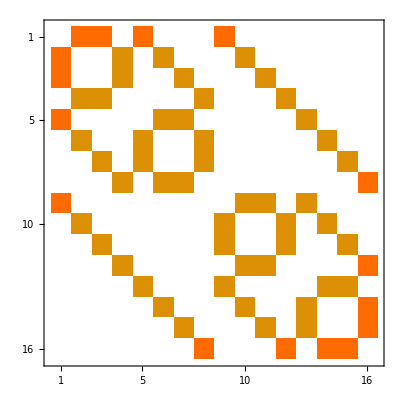

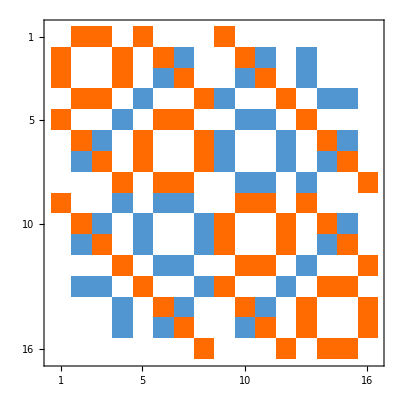

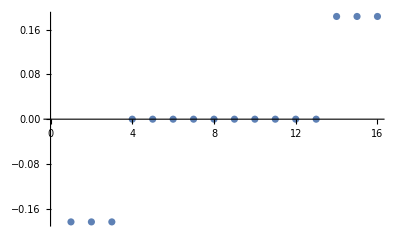

{-0.183503,-0.183503,-0.183503,-3.66653×10^-17,-1.47069×10^-17,0.,0.,2.9547×10^-18,6.21687×10^-18,1.67651×10^-17,1.83547×10^-17,4.00755×10^-17,6.42061×10^-17,0.183503,0.183503,0.183503}

```mathematica
M=4;
g=1;
SingletStates = Table[(1/Sqrt[Binomial[M, PartN]])Sum[If[Total[IntegerDigits[n, 2]]==PartN, SparseArray[Table[If[i==n, 1, 0], {i, 0, 2^M-1}]], 0], {n, 0, 2^M-1}], {PartN, 0, M}];
LzLpLz=(1/Sqrt[6])Sum[FullSigma[4, l, M], {l, 0, M-1}]+(3-Sqrt[6])/48 Sum[FullSigma[3, l, M], {l, 0, M-1}].Sum[FullSigma[4, l, M], {l, 0, M-1}].Sum[FullSigma[3, l, M], {l, 0, M-1}]//FullSimplify;
LpLpLm=1/6 (9-2 √6)Sum[FullSigma[4, l, M], {l, 0, M-1}]+1/12 (-3+√6)Sum[Sum[FullSigma[If[k==1, 5, 4], l, M], {l, 0, M-1}].Sum[FullSigma[If[k==2, 5, 4], l, M], {l, 0, M-1}].Sum[FullSigma[If[k==3, 5, 4], l, M], {l, 0, M-1}], {k, 2,2}]//FullSimplify;
MatrixPlot[LzLpLz+ConjugateTranspose[LzLpLz]]
MatrixPlot[LpLpLm+ConjugateTranspose[LpLpLm]//FullSimplify]
(*ListPlot[{Sort[Eigenvalues[ HKinetic[M, g]+1/(2g^2)(LzLpLz+ConjugateTranspose[LzLpLz])//N], Less], Sort[Eigenvalues[HKinetic[M, g]+1/(2g^2)(LpLpLm+ConjugateTranspose[LpLpLm])//N], Less]}]*)
ListPlot[Sort[Eigenvalues[ (HKinetic[M, g]+1/(2g^2)(LzLpLz+ConjugateTranspose[LzLpLz]))-(HKinetic[M, g]+1/(2g^2)(LpLpLm+ConjugateTranspose[LpLpLm]))//N], Less]]
Sort[Eigenvalues[ (HKinetic[M, g]+1/(2g^2)(LzLpLz+ConjugateTranspose[LzLpLz]))-(HKinetic[M, g]+1/(2g^2)(LpLpLm+ConjugateTranspose[LpLpLm]))//N], Less]
```

```mathematica
Sort[Eigenvalues[ HKinetic[M, g]+1/(g^2)(LzLpLz+ConjugateTranspose[LzLpLz])//N], Less]
```

{-0.00455129,-0.00160247,-0.00160247,-0.00160247,-8.8384×10^-18,-4.75438×10^-18,0.0391724,0.04,0.04,0.04,0.0416025,0.0416025,0.0416025,0.0437151,0.160828,0.160836}

```mathematica
Sort[Eigenvalues[Table[SingletStates[[i]].(HKinetic[M, g]+1/(g^2)(LzLpLz+ConjugateTranspose[LzLpLz])//N).SingletStates[[j]], {i, 1, M+1}, {j, 1, M+1}]], Less]
```

{-0.00455129,0.0391724,0.0437151,0.160828,0.160836}

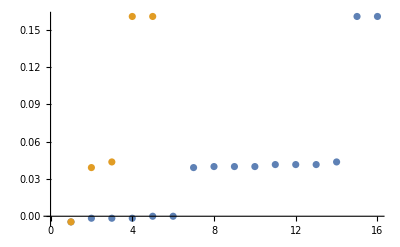

```mathematica
ListPlot[{%64, %67}]
```

```mathematica
LzLpLzSub=Table[SingletStates[[i]].LzLpLz.SingletStates[[j]], {i, 1, M+1}, {j, 1, M+1}]//FullSimplify;
LpLpLmSub=Table[SingletStates[[i]].LpLpLm.SingletStates[[j]], {i, 1, M+1}, {j, 1, M+1}]//FullSimplify;
MatrixForm[LzLpLzSub]
MatrixForm[LpLpLmSub]
```

(0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0)

(0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0)

```mathematica
Solve[{2a+8b==1, Sqrt[6]a+6Sqrt[6]b==1}, {a,b}]
```

{{a→1/6 (9-2 √6),b→1/12 (-3+√6)}}

## Using only 3 qubits for M=4

### 4^3 = 64 8x8 basis matrices

```mathematica
BasMat = Flatten[Table[KroneckerProduct[Sigma[i], Sigma[j], Sigma[k]], {i, 0, 3}, {j, 0, 3}, {k, 0, 3}], 2];
BasMatPM = Flatten[Table[KroneckerProduct[Sigma[i], Sigma[j], Sigma[k]], {i, {0, 3, 4, 5}}, {j, {0, 3, 4, 5}}, {k, {0, 3, 4, 5}}], 2];
```

```mathematica
coef=Array[a, 4^3];
```

### U operator

```mathematica
U8=Table[If[1<=i≤6&& j==i+1, 1, 0], {i, 1, 8}, {j, 1, 8}];
soln=Solve[U8==Sum[a[i] BasMatPM[[i]], {i, 1, 64}], coef];
Select[Table[{BaseForm[i-1, 4], (coef/.soln[[1]])[[i]]}, {i, 1, 64}], ! MemberQ[#, 0]&]
MatrixForm[Sum[(coef/.soln[[1]])[[i]] BasMatPM[[i]], {i, 1, 64}]]
```

{{2_4,3/4},{12_4,1/4},{23_4,1},{102_4,1/4},{112_4,-1/4},{233_4,1}}

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### U^\dag operator

```mathematica
U8dag=Table[If[2<=i≤5 && j==i-1, 1, 0], {i, 1, 8}, {j, 1, 8}];
soln=Solve[U8dag==Sum[a[i] BasMatPM[[i]], {i, 1, 64}], coef];
Select[Table[{BaseForm[i-1, 4], (coef/.soln[[1]])[[i]]}, {i, 1, 64}], ! MemberQ[#, 0]&]
MatrixForm[Sum[(coef/.soln[[1]])[[i]] BasMatPM[[i]], {i, 1, 64}]]
```

{{3_4,1/2},{32_4,1/2},{103_4,1/2},{132_4,1/2},{322_4,1}}

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### E operator

```mathematica
Eop=Table[If[1<=i≤5 && j==i, (i-3), 0], {i, 1, 8}, {j, 1, 8}];
soln=Solve[Eop==Sum[a[i] BasMatPM[[i]], {i, 1, 64}], coef];
Select[Table[{BaseForm[i-1, 4], (coef/.soln[[1]])[[i]]}, {i, 1, 64}], ! MemberQ[#, 0]&]
MatrixForm[Sum[(coef/.soln[[1]])[[i]] BasMatPM[[i]], {i, 1, 64}]]
```

{{10_4,-1/4},{11_4,1/4},{100_4,-1/2},{101_4,-1/2},{110_4,-3/4},{111_4,-1/4}}

(-2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
MatrixForm[Commutator[Table[If[1<=i≤5 && j==i, (i-3), 0], {i, 1, 8}, {j, 1, 8}], U8]]
```

(0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
MatrixForm[Commutator[U8, U8dag]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
MatrixForm[MatrixPower[Table[If[(2<=i≤5|| 7<=i)&& j==i-1, 1, 0], {i, 1, 8}, {j, 1, 8}],1]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
BasMatPM2 = Flatten[Table[KroneckerProduct[Sigma[i], Sigma[j]], {i, {0, 3, 4, 5}}, {j, {0, 3, 4, 5}}], 1];
coef=Array[a, 4^2];
```

```mathematica
U4=Table[If[(1<=i≤2)&& j==i+1, 1, 0], {i, 1, 4}, {j, 1, 4}];
soln=Solve[U4==Sum[a[i] BasMatPM2[[i]], {i, 1, 16}], coef]
Select[Table[{BaseForm[i-1, 4], (coef/.soln[[1]])[[i]]}, {i, 1, 16}], ! MemberQ[#, 0]&]
MatrixForm[Sum[(coef/.soln[[1]])[[i]] BasMatPM2[[i]], {i, 1, 16}]]
```

{{a[1]→0,a[2]→0,a[3]→1/2,a[4]→0,a[5]→0,a[6]→0,a[7]→1/2,a[8]→0,a[9]→0,a[10]→0,a[11]→0,a[12]→1,a[13]→0,a[14]→0,a[15]→0,a[16]→0}}

{{2_4,1/2},{12_4,1/2},{23_4,1}}

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
E4=Table[If[1<=i≤3 && j==i, (i-2), 0], {i, 1, 4}, {j, 1, 4}];
soln=Solve[E4==Sum[a[i] BasMatPM2[[i]], {i, 1, 16}], coef]
Select[Table[{BaseForm[i-1, 4], (coef/.soln[[1]])[[i]]}, {i, 1, 16}], ! MemberQ[#, 0]&]
MatrixForm[Sum[(coef/.soln[[1]])[[i]] BasMatPM2[[i]], {i, 1, 16}]]
```

{{a[1]→0,a[2]→0,a[3]→0,a[4]→0,a[5]→-1/2,a[6]→-1/2,a[7]→0,a[8]→0,a[9]→0,a[10]→0,a[11]→0,a[12]→0,a[13]→0,a[14]→0,a[15]→0,a[16]→0}}

{{10_4,-1/2},{11_4,-1/2}}

(-1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0)

```mathematica
MatrixForm[KroneckerProduct[Sigma[4],Sigma[5]]+KroneckerProduct[Sigma[5],Sigma[4]]]
```

(0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0)